# ^163Lu - Double-energy-shift fit approach

## Fitting the excitation energies using a novel approach with ϵ=(ϵ_TSD2,ϵ_TSD4) upward shifts in the wobbling energy (theoretical values)

## The parameter set is determined in such a way that the E_RMS has the smallest possible value

## Experimental Data

```mathematica
DATA1={{8.5,0.1966},{10.5,0.4597},{12.5,0.7746},{14.5,1.1609},{16.5,1.6112},{18.5,2.1265},{20.5,2.7051},{22.5,3.3441},{24.5,4.0411},{26.5,4.7937},{28.5,5.5992},{30.5,6.457},{32.5,7.3667},{34.5,8.3293},{36.5,9.3458},{38.5,10.4169},{40.5,11.5431},{42.5,12.7224},{44.5,13.9491},{46.5,15.2181},{48.5,16.5221}};
DATA2={{13.5,1.3394},{15.5,1.7467},{17.5,2.2184},{19.5,2.7527},{21.5,3.3484},{23.5,4.003},{25.5,4.7143},{27.5,5.4805},{29.5,6.3004},{31.5,7.1733},{33.5,8.0998},{35.5,9.08},{37.5,10.1147},{39.5,11.2036},{41.5,12.3466},{43.5,13.5441},{45.5,14.7911}};
DATA3={{16.5,2.1237},{18.5,2.6293},{20.5,3.1973},{22.5,3.8243},{24.5,4.5094},{26.5,5.2506},{28.5,6.0465},{30.5,6.8963},{32.5,7.7988},{34.5,8.7546},{36.5,9.7638},{38.5,10.8268},{40.5,11.9392},{42.5,13.0861}};
DATA4={{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};
SPINS=Table[i,{i,6.5,48.5,1}];
```

## Analytic formulas for the excitation energies

```mathematica
B[I_,j_,A1_,A2_,A3_,V_,γ_]:=-(((2I-1)(A3-A1)+2j*A1)*((2I-1)(A2-A1)+2j*A1)+8A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2j-1)(A2-A1)+2I*A1+V(2j-1)/(j(j+1))2 √3 Sin[γ*π/180]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=(((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4I*j*A3^2)*(((2I-1)(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[γ*π/180])-4I*j*A2^2);
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)/2(I+j)+A1(I-j)^2-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B[I,j,A1,A2,A3,V,γ]-(B[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B[I,j,A1,A2,A3,V,γ]+(B[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
EWobb[n1_,n2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](n1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](n2+1/2);
IF[I_]:=1/(2I);
```

## Wobbling bands used in 2ϵ-fit

```mathematica
TSD1[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD2[I_,A1_,A2_,A3_,V_,γ_,shift_]:=(EWobb[0,0,I,6.5,A1,A2,A3,V,γ]+shift)-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD3[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD4[I_,A1_,A2_,A3_,V_,γ_,shift_]:=(EWobb[0,0,I,6.5,A1,A2,A3,V,γ]+shift)-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
```

## Fit parameters: numerical values from CXX (imported)

```mathematica
a1=1/(2*72);a2=1/(2*15);a3=1/(2*7);v=2.1;gm=22;shiftTSD2=0.3;shiftTSD4=0.6;
```

## RMS Computation

```mathematica
RMS[tsd1_,tsd2_,tsd3_,tsd4_,shift2_,shift4_]:=Sqrt[1/63(Sum[(DATA1[[i,2]]-tsd1[DATA1[[i,1]],a1,a2,a3,v,gm])^2,{i,1,Length[DATA1]}]+Sum[(DATA2[[i,2]]-tsd2[DATA2[[i,1]],a1,a2,a3,v,gm,shift2])^2,{i,1,Length[DATA2]}]+Sum[(DATA3[[i,2]]-tsd3[DATA3[[i,1]],a1,a2,a3,v,gm])^2,{i,1,Length[DATA3]}]+Sum[(DATA4[[i,2]]-tsd4[DATA4[[i,1]],a1,a2,a3,v,gm,shift4])^2,{i,1,Length[DATA4]}])];
```

```mathematica
rmsValue=N[RMS[TSD1,TSD2,TSD3,TSD4,shiftTSD2,shiftTSD4]]
```

0.0794873

## Excitation energies - Tabular view

```mathematica
params[spin_,a1_,a2_,a3_,v_,gm_]:={Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3→``:``:``\nV=`` γ=(``)^o\nE_RMS=``\nϵ_TSD2=`` ϵ_TSD4=``"][IF[a1],IF[a2],IF[a3],v,gm,rmsValue,shiftTSD2,shiftTSD4],Black,Bold,22,FontFamily->"Times New Roman"],SpanFromLeft};
header[TSD_]:={Style["I [ℏ]",Black,Bold,18,FontFamily->"Times New Roman"],Style[StringTemplate["E_(exc ;  Exp.)^(``) [MeV]"][TSD],Black,Bold,18,FontFamily->"Times New Roman"],Style[StringTemplate["E_(exc ;  Th.)^(``) [MeV]"][TSD],Black,Bold,18,FontFamily->"Times New Roman"]};
```

```mathematica
paramTable=Table[{Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3→``:``:``"][IF[a1],IF[a2],IF[a3]],Black,Bold,22,FontFamily->"Times New Roman"],Style[StringTemplate["V=`` γ=(``)^o"][v,gm],Black,Bold,22,FontFamily->"Times New Roman"],Style[StringTemplate["E_RMS=``"][rmsValue],Black,Bold,22,FontFamily->"Times New Roman"],Style[StringTemplate["ϵ_TSD2=`` ϵ_TSD4=``"][shiftTSD2,shiftTSD4],Black,Bold,22,FontFamily->"Times New Roman"]},{i,1,1}];
```

```mathematica
paramList={{Style["Fit Parameters",Black,Bold,22,FontFamily->"Times New Roman"]},{Style["Double ϵ-shift approach",Black,Bold,Italic,15,FontFamily->"Times New Roman"]}};
Do[AppendTo[paramList,{paramTable[[1,i]]}],{i,1,Length[paramTable[[1]]]}]
Grid[paramList,Frame->All,Background->{LightBlue,{1->LightGreen}}]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/double-shift_parameters.png",Grid[paramList,Frame->All,Background->{LightBlue,{1->LightGreen}}]];
```

Fit Parameters
Double ϵ-shift approach
ℐ_1:ℐ_2:ℐ_3→72:15:7
V=2.1 γ=22^o
E_RMS=0.0794873
ϵ_TSD2=0.3 ϵ_TSD4=0.6

## TSD1

```mathematica
table1=Table[{DATA1[[i,1]],DATA1[[i,2]],TSD1[DATA1[[i,1]],a1,a2,a3,v,gm]},{i,1,Length[DATA1]}];
AppendTo[table1,params[12.5,a1,a2,a3,v,gm]];
PrependTo[table1,header[TSD1]];
Grid[table1,Frame->All,Background->{{{LightBlue,LightGray,LightGray}},{1->LightGreen,-1->LightGreen}}]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/tsd1_data.pdf",Grid[table1,Frame->All,Background->{{{LightBlue,LightGray,LightGray}},{1->LightGreen,-1->LightGreen}}]];
```

I [ℏ] | E_(exc ;  Exp.)^TSD1 [MeV] | E_(exc ;  Th.)^TSD1 [MeV]
8.5 | 0.1966 | 0.230329
10.5 | 0.4597 | 0.516162
12.5 | 0.7746 | 0.857522
14.5 | 1.1609 | 1.25441
16.5 | 1.6112 | 1.70683
18.5 | 2.1265 | 2.21478
20.5 | 2.7051 | 2.77826
22.5 | 3.3441 | 3.39726
24.5 | 4.0411 | 4.07178
26.5 | 4.7937 | 4.80183
28.5 | 5.5992 | 5.5874
30.5 | 6.457 | 6.42849
32.5 | 7.3667 | 7.3251
34.5 | 8.3293 | 8.27724
36.5 | 9.3458 | 9.28491
38.5 | 10.4169 | 10.3481
40.5 | 11.5431 | 11.4668
42.5 | 12.7224 | 12.6411
44.5 | 13.9491 | 13.8708
46.5 | 15.2181 | 15.1561
48.5 | 16.5221 | 16.497
ℐ_1:ℐ_2:ℐ_3→72:15:7
V=2.1 γ=22^o
E_RMS=0.0794873
ϵ_TSD2=0.3 ϵ_TSD4=0.6 |  |

## TSD2

```mathematica
table2=Table[{DATA2[[i,1]],DATA2[[i,2]],TSD2[DATA2[[i,1]],a1,a2,a3,v,gm,shiftTSD2]},{i,1,Length[DATA2]}];
AppendTo[table2,params[15.5,a1,a2,a3,v,gm]];
PrependTo[table2,header[TSD2]];
Grid[table2,Frame->All,Background->{{{LightBlue,LightGray,LightGray}},{1->LightGreen,-1->LightGreen}}]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/tsd2_data.pdf",Grid[table2,Frame->All,Background->{{{LightBlue,LightGray,LightGray}},{1->LightGreen,-1->LightGreen}}]];
```

I [ℏ] | E_(exc ;  Exp.)^TSD2 [MeV] | E_(exc ;  Th.)^TSD2 [MeV]
13.5 | 1.3394 | 1.34903
15.5 | 1.7467 | 1.77368
17.5 | 2.2184 | 2.25387
19.5 | 2.7527 | 2.78958
21.5 | 3.3484 | 3.38082
23.5 | 4.003 | 4.02758
25.5 | 4.7143 | 4.72986
27.5 | 5.4805 | 5.48767
29.5 | 6.3004 | 6.301
31.5 | 7.1733 | 7.16986
33.5 | 8.0998 | 8.09423
35.5 | 9.08 | 9.07413
37.5 | 10.1147 | 10.1096
39.5 | 11.2036 | 11.2005
41.5 | 12.3466 | 12.347
43.5 | 13.5441 | 13.549
45.5 | 14.7911 | 14.8065
ℐ_1:ℐ_2:ℐ_3→72:15:7
V=2.1 γ=22^o
E_RMS=0.0794873
ϵ_TSD2=0.3 ϵ_TSD4=0.6 |  |

## TSD3

```mathematica
table3=Table[{DATA3[[i,1]],DATA3[[i,2]],TSD3[DATA3[[i,1]],a1,a2,a3,v,gm]},{i,1,Length[DATA3]}];
AppendTo[table3,params[18.5,a1,a2,a3,v,gm]];
PrependTo[table3,header[TSD3]];
Grid[table3,Frame->All,Background->{{{LightBlue,LightGray,LightGray}},{1->LightGreen,-1->LightGreen}}]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/tsd3_data.pdf",Grid[table3,Frame->All,Background->{{{LightBlue,LightGray,LightGray}},{1->LightGreen,-1->LightGreen}}]];
```

I [ℏ] | E_(exc ;  Exp.)^TSD3 [MeV] | E_(exc ;  Th.)^TSD3 [MeV]
16.5 | 2.1237 | 2.04238
18.5 | 2.6293 | 2.57396
20.5 | 3.1973 | 3.15888
22.5 | 3.8243 | 3.7974
24.5 | 4.5094 | 4.48976
26.5 | 5.2506 | 5.23613
28.5 | 6.0465 | 6.0367
30.5 | 6.8963 | 6.89161
32.5 | 7.7988 | 7.80099
34.5 | 8.7546 | 8.76495
36.5 | 9.7638 | 9.7836
38.5 | 10.8268 | 10.857
40.5 | 11.9392 | 11.9853
42.5 | 13.0861 | 13.1685
ℐ_1:ℐ_2:ℐ_3→72:15:7
V=2.1 γ=22^o
E_RMS=0.0794873
ϵ_TSD2=0.3 ϵ_TSD4=0.6 |  |

## TSD4

```mathematica
table4=Table[{DATA4[[i,1]],DATA4[[i,2]],TSD4[DATA4[[i,1]],a1,a2,a3,v,gm,shiftTSD4]},{i,1,Length[DATA4]}];
AppendTo[table4,params[15.5,a1,a2,a3,v,gm]];
PrependTo[table4,header[TSD4]];
Grid[table4,Frame->All,Background->{{{LightBlue,LightGray,LightGray}},{1->LightGreen,-1->LightGreen}}]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/tsd4_data.pdf",Grid[table4,Frame->All,Background->{{{LightBlue,LightGray,LightGray}},{1->LightGreen,-1->LightGreen}}]];
```

I [ℏ] | E_(exc ;  Exp.)^TSD4 [MeV] | E_(exc ;  Th.)^TSD4 [MeV]
23.5 | 4.58 | 4.32758
25.5 | 5.2251 | 5.02986
27.5 | 5.9273 | 5.78767
29.5 | 6.6819 | 6.601
31.5 | 7.4919 | 7.46986
33.5 | 8.3573 | 8.39423
35.5 | 9.2778 | 9.37413
37.5 | 10.2535 | 10.4096
39.5 | 11.2851 | 11.5005
41.5 | 12.3701 | 12.647
ℐ_1:ℐ_2:ℐ_3→72:15:7
V=2.1 γ=22^o
E_RMS=0.0794873
ϵ_TSD2=0.3 ϵ_TSD4=0.6 |  |

## Excitation energies - plots

## TSD1

```mathematica
StringTemplate["^(``)``\n``"][163,"Lu",TSD1]
```

^163Lu
TSD1

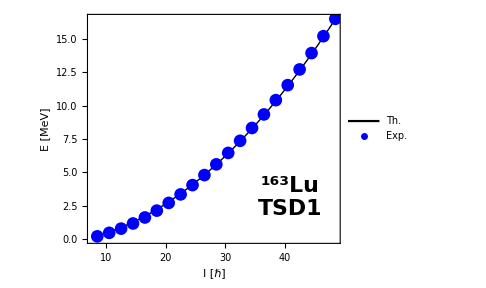

```mathematica
lp1=ListPlot[{Table[{DATA1[[i,1]],TSD1[DATA1[[i,1]],a1,a2,a3,v,gm]},{i,1,Length[DATA1]}],DATA1},Frame->True,Axes->False,PlotStyle->{{Black,Thick},{Blue}},Joined->{True,False},PlotMarkers->{{None,1},{"●",13}},AspectRatio->0.8,FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","E [MeV]"},PlotLegends->Placed[{"Th.","Exp."},{0.2,0.8}],LabelStyle->{18,Black,Bold,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["^(``)``\n``"][163,"Lu",TSD1],Black,Italic,22,Bold,FontFamily->"Times New Roman"],Scaled[{0.8,0.2}]],ImageSize->Medium];
Show[lp1]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/DoubleShift_TSD1.pdf",Show[lp1]];
```

## TSD2

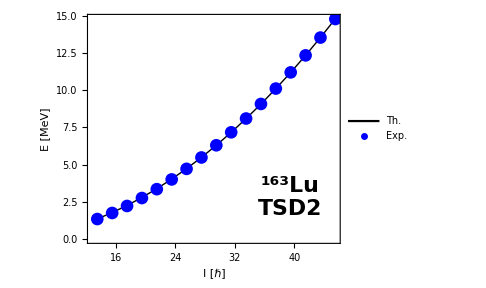

```mathematica
lp2=ListPlot[{Table[{DATA2[[i,1]],TSD2[DATA2[[i,1]],a1,a2,a3,v,gm,shiftTSD2]},{i,1,Length[DATA2]}],DATA2},Frame->True,Axes->False,PlotStyle->{{Black,Thick},{Blue}},Joined->{True,False},PlotMarkers->{{None,1},{"●",13}},AspectRatio->0.8,FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","E [MeV]"},PlotLegends->Placed[{"Th.","Exp."},{0.2,0.8}],LabelStyle->{18,Black,Bold,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["^(``)``\n``"][163,"Lu",TSD2],Black,Italic,22,Bold,FontFamily->"Times New Roman"],Scaled[{0.8,0.2}]],ImageSize->Medium];
Show[lp2]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/DoubleShift_TSD2.pdf",Show[lp2]];
```

## TSD3

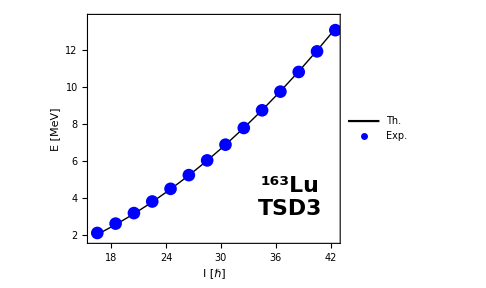

```mathematica
lp3=ListPlot[{Table[{DATA3[[i,1]],TSD3[DATA3[[i,1]],a1,a2,a3,v,gm]},{i,1,Length[DATA3]}],DATA3},Frame->True,Axes->False,PlotStyle->{{Black,Thick},{Blue}},Joined->{True,False},PlotMarkers->{{None,1},{"●",13}},AspectRatio->0.8,FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","E [MeV]"},PlotLegends->Placed[{"Th.","Exp."},{0.2,0.8}],LabelStyle->{18,Black,Bold,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["^(``)``\n``"][163,"Lu",TSD3],Black,Italic,22,Bold,FontFamily->"Times New Roman"],Scaled[{0.8,0.2}]],ImageSize->Medium,PlotRange->{1.8,13.7}];
Show[lp3]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/DoubleShift_TSD3.pdf",Show[lp3]];
```

## TSD4

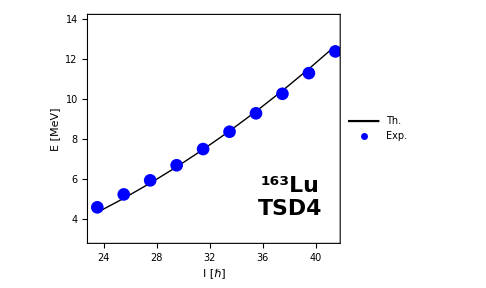

```mathematica
lp4=ListPlot[{Table[{DATA4[[i,1]],TSD4[DATA4[[i,1]],a1,a2,a3,v,gm,shiftTSD4]},{i,1,Length[DATA4]}],DATA4},Frame->True,Axes->False,PlotStyle->{{Black,Thick},{Blue}},Joined->{True,False},PlotMarkers->{{None,1},{"●",13}},AspectRatio->0.8,FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","E [MeV]"},PlotLegends->Placed[{"Th.","Exp."},{0.2,0.8}],LabelStyle->{18,Black,Bold,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["^(``)``\n``"][163,"Lu",TSD4],Black,Italic,22,Bold,FontFamily->"Times New Roman"],Scaled[{0.8,0.2}]],ImageSize->Medium,PlotRange->{3,14}];
Show[lp4]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/DoubleShift_TSD4.pdf",Show[lp4]];
```

### Grid with the plots

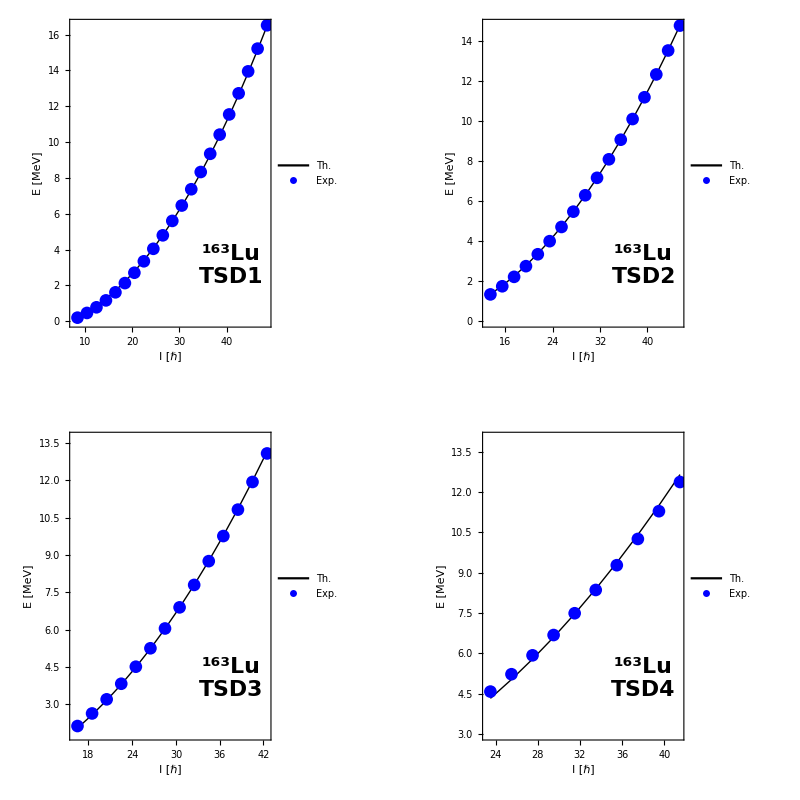

```mathematica
GraphicsGrid[{{lp1,lp2},{lp3,lp4}},ImageSize->Scaled[0.7],Frame->All]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/double-shift/DoubleShift_energiesGrid.png",GraphicsGrid[{{lp1,lp2},{lp3,lp4}},ImageSize->Scaled[1],Frame->All]];
```